```mathematica
ρ={{ρ00[t],ρ01[t],ρ02[t]},{ρ10[t],ρ11[t],ρ12[t]},{ρ20[t],ρ21[t],ρ22[t]}}
```

{{ρ00[t],ρ01[t],ρ02[t]},{ρ10[t],ρ11[t],ρ12[t]},{ρ20[t],ρ21[t],ρ22[t]}}

```mathematica
ρinitial = {{1,0,0},{0,0,0},{0,0,0}}
ρinitial = ρinitial/Tr[ρinitial]
```

{{1,0,0},{0,0,0},{0,0,0}}

{{1,0,0},{0,0,0},{0,0,0}}

```mathematica
meq[l_,ρ_]:=l.ρ.ConjugateTranspose[l]-1/2(ρ.ConjugateTranspose[l].l+ ConjugateTranspose[l].l.ρ)
```

```mathematica
lr10 = Sqrt[Γr10]{{0,1,0},{0,0,0},{0,0,0}};
lr21 = Sqrt[Γr21]{{0,0,0},{0,0,1},{0,0,0}};
lr20 = Sqrt[Γr20]{{0,0,1},{0,0,0},{0,0,0}};
lϕ10 = Sqrt[Γϕ10/2]{{1,0,0},{0,-1,0},{0,0,0}};
lϕ20 = Sqrt[Γϕ21/2]{{1,0,0},{0,0,0},{0,0,-1}};
lϕ21 = Sqrt[Γϕ20/2]{{0,0,0},{0,1,0},{0,0,-1}};
```

$Aborted

```mathematica
gaussianPulse[t0_,Δ_] := 1/Sqrt[2π]Exp[-((t-t0)/Δ)^2/2]
```

```mathematica
Remove[drive];
drive[ϕ_] := {{0,Conjugate[ϕ],0},{ϕ,0,Conjugate[ϕ]Sqrt[2]},{0,Conjugate[ϕ]Sqrt[2],0}}
h = 2*drive[1Exp[I π/2]]*gaussianPulse[50,4.95,1]/π+{{0,0,0},{0,0,0},{0,0,-2π 0.24}}
```

{{0,-(ⅈ √2 ⅇ^(-0.0204061 (-50+t)^2))/π^(3/2),0},{(ⅈ √2 ⅇ^(-0.0204061 (-50+t)^2))/π^(3/2),0,-(2 ⅈ ⅇ^(-0.0204061 (-50+t)^2))/π^(3/2)},{0,-(2 ⅈ ⅇ^(-0.0204061 (-50+t)^2))/π^(3/2),-1.50796}}

```mathematica
relaxationrates = {Γr10->1./5000,Γr21->1./5000.*Sqrt[2],Γr20->0,Γϕ10->1./5000.,Γϕ21->1./5000.,Γϕ20->1./5000.};
```

```mathematica
meq[lϕ10,ρ] // MatrixForm
```

(0 | -√Γϕ10 Conjugate[√Γϕ10] ρ01[t] | -1/4 √Γϕ10 Conjugate[√Γϕ10] ρ02[t]
-√Γϕ10 Conjugate[√Γϕ10] ρ10[t] | 0 | -1/4 √Γϕ10 Conjugate[√Γϕ10] ρ12[t]
-1/4 √Γϕ10 Conjugate[√Γϕ10] ρ20[t] | -1/4 √Γϕ10 Conjugate[√Γϕ10] ρ21[t] | 0)

```mathematica
Tr[meq[lr1,ρ]]
```

0

```mathematica
ρflat = Flatten[ρ];
ρinitialflat = Flatten[ρinitial];
lflat = Flatten[-I (h.ρ-ρ.h)+ meq[lr10,ρ]+ meq[lr21,ρ]+ meq[lr20,ρ]+ meq[lϕ10,ρ]+meq[lϕ21,ρ]+meq[lϕ20,ρ]];
eqs =SetPrecision[Map[D[ρflat[[#]],t]== lflat[[#]]&,Range[1,Length[ρflat]]] /. relaxationrates,60];
bcs = SetPrecision[Map[ρflat[[#]] == ρinitialflat[[#]]/.{t->0} &,Range[1,Length[ρflat]]],60];
solution = NDSolve[Join[eqs,bcs],Map[ρflat[[#]]&,Range[1,Length[ρflat]]],{t,0,100},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35,MaxSteps->Infinity];
```

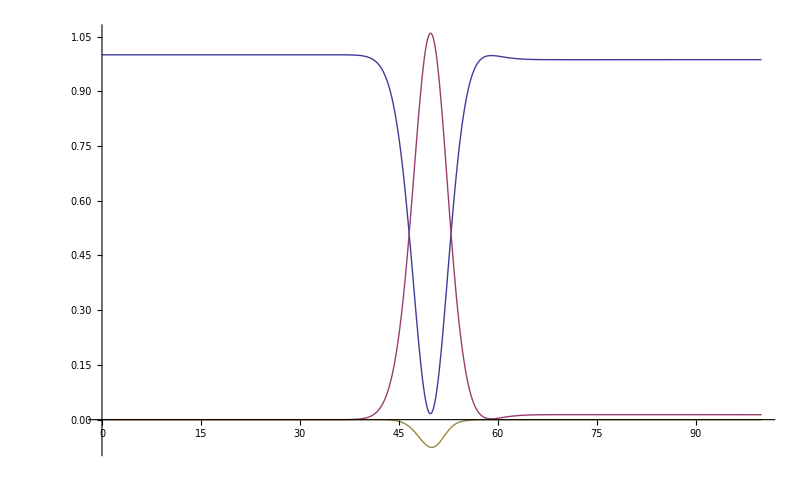

```mathematica
Plot[{Re[solution[[1]][[1]][[2]]],Re[solution[[1]][[5]][[2]]],Re[solution[[1]][[9]][[2]]]},{t,0,100},PlotRange->Full]
```

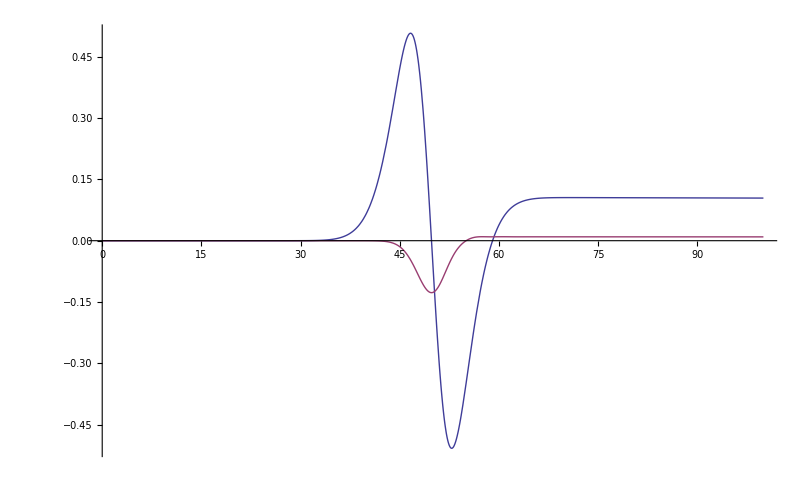

```mathematica
Plot[{Re[solution[[1]][[2]][[2]]],Im[solution[[1]][[2]][[2]]]},{t,0,100},PlotRange->Full]
```

```mathematica
1/Sqrt[2π]NIntegrate[Exp[-((t-5)/5.)^2/2],{t,-100,100}]
```

5.

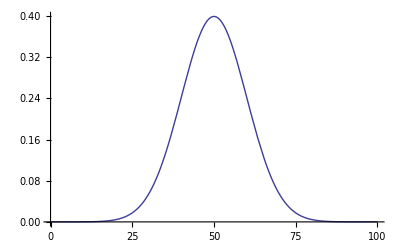

```mathematica
Plot[gaussianPulse[50,10],{t,0,100}]
```